This notebook produces plots of the orbits generated by local complementation orbit up and including to 9 qubits, when isomorphic graphs are considered equal.

This work refers to “Mapping graph state orbits under local complementation”, https://arxiv.org/abs/1910.03969. Please see this work for assosciated documentation.

You can choose to import from .mx or .csv. Importing data from .mx is faster, but may not be possible on older versions of Mathematica. Importing from .csv is broken up into qubit number as it can be slow for large number of qubits. Feel free to just import the qubit number you are interested in.

## Load data

#### Constants & Data

Data is organised into nested lists, where the first index, i, gives the qubit number and the second j, indexes the orbit, which are in order as per the canonical listing of Hein, Danielsen, et al. (see references 11, 16 and 17 of the manuscript).

```mathematica
SetDirectory[NotebookDirectory[]];
goodcolours=ColorData[97,"ColorList"];

(* Graph state display options*)
defcol=ColorData[97,"ColorList"][[7]];
graphsize=100;
vertexsize=0.30;
edgethickness =0.024;
impad=10;

(* precompiled import for csv *)
len4={2,4};
len5={2,6,10,3};
len6={2,6,4,16,10,25,5,5,21,16,2};
len7={2,6,6,16,10,10,16,44,44,14,66,10,10,21,26,36,28,72,114,56,92,57,33,9,46,9};
len8={2,6,6,16,4,16,10,16,44,16,44,10,25,44,44,26,120,66,14,25,120,72,172,10,10,10,21,10,44,66,26,26,28,44,132,114,72,72,198,56,28,10,56,66,72,63,66,176,76,194,352,154,542,300,214,14,66,66,6,57,28,17,72,87,114,372,70,264,542,156,174,542,262,802,117,10,37,36,7,103,46,170,74,340,254,433,476,28,9,39,46,208,298,24,267,4,22,46,28,7,51};
len9={2,6,6,16,6,16,10,10,16,44,16,44,16,16,44,44,44,44,26,120,10,44,44,66,26,66,120,14,44,120,26,44,120,72,120,112,328,72,66,120,328,72,328,174,18,196,464,10,16,10,21,16,44,66,26,36,26,44,26,28,44,132,114,5,44,72,44,28,72,132,26,120,372,72,72,75,56,28,56,44,26,66,132,114,176,120,28,120,72,66,120,372,352,76,542,56,176,352,154,120,176,42,72,76,72,154,372,352,196,542,300,76,120,352,72,328,194,198,194,484,542,300,984,66,46,74,328,208,352,968,542,300,984,1498,828,154,91,240,488,420,1428,498,5,36,132,66,75,66,114,14,204,24,57,28,87,72,132,26,72,372,114,372,114,112,542,264,94,87,132,198,176,46,198,264,372,1052,91,156,542,174,38,72,132,352,204,186,198,528,220,1052,296,300,754,754,76,194,188,352,28,220,372,372,1052,544,324,1008,312,1052,1052,1052,1056,1550,1534,220,186,1476,1498,924,763,156,308,98,542,272,300,984,754,3004,222,426,105,1436,704,1472,474,1508,1498,2104,4246,1328,28,37,21,89,14,46,57,186,170,142,170,74,340,76,204,198,102,542,306,320,484,782,38,36,204,220,198,372,542,1052,340,1052,1096,1594,94,192,178,476,542,596,920,3004,952,1544,806,202,1334,156,504,528,1052,462,340,192,542,542,476,1534,754,484,1564,952,1534,1550,1550,3004,1578,116,58,452,283,462,3088,908,399,2198,4306,4402,2270,2292,4378,2684,9,63,100,46,42,75,85,174,340,119,182,188,1578,460,220,166,1148,24,24,170,160,784,564,168,494,1536,1594,1610,1578,768,494,1568,476,1610,1626,124,484,1114,1628,814,1594,66,952,356,952,126,840,2214,4470,818,2262,8836,726,1129,1384,1398,305,844,4514,2336,476,153,27,70,46,162,170,276,340,220,494,1610,128,494,988,736,1348,227,608,1246,541,4580,4538,1384,2408,744,4594,4592,2366,344,870,119,115,99,30,269,538,238,68,772,1216,630,1414,672,836,4670,80,1464,1478,862,278,129,94,893,609,242,21,567};

lenorbitsCi={{1},{1},{1},len4,len5,len6,len7,len8,len9};


fourCiorbits=Range[2];
fourCigraphlists=Table[0,{i,Range[2]},{j,len4[[i]]}];
four=4;

fiveCiorbits=Range[4];
fiveCigraphlists=Table[0,{i,Range[4]},{j,len5[[i]]}];
five=5;

sixCiorbits=Range[11];
sixCigraphlists=Table[0,{i,Range[11]},{j,len6[[i]]}];
six=6;

sevenCiorbits=Range[26];
sevenCigraphlists=Table[0,{i,Range[26]},{j,len7[[i]]}];
seven=7;

eightCiorbits=Range[101];
eightCigraphlists=Table[0,{i,Range[101]},{j,len8[[i]]}];
eight=8;

nineCiorbits=Range[440];
nineCigraphlists=Table[0,{i,Range[440]},{j,len9[[i]]}];
nine=9;

(* number of edges in each orbit *)
noedgorbitsCi={{0},{0},{2},{2,5},{2,9,19,3},{2,9,5,34,20,58,8,9,47,29,2},{2,9,9,34,19,20,35,114,118,30,191,20,21,47,68,98,70,206,336,157,271,164,80,16,109,16},{2,9,9,34,5,34,20,35,114,35,118,20,58,118,118,66,372,201,31,62,382,218,593,20,20,21,47,21,122,197,69,68,70,120,402,336,220,222,678,157,72,21,164,198,219,182,202,616,230,659,1264,506,2021,1056,749,34,205,193,12,164,77,41,215,267,364,1324,208,974,2025,528,576,2043,967,3044,342,22,102,97,12,339,121,571,224,1172,858,1586,1706,75,16,103,124,758,1076,56,885,5,46,126,60,16,134},{2,9,9,34,9,34,19,20,35,114,35,118,35,35,114,118,118,118,66,372,20,118,118,201,66,191,388,31,121,382,67,121,382,218,382,366,1180,222,201,394,1220,222,1208,612,41,692,1850,20,36,21,47,37,122,197,68,98,69,124,68,70,120,402,336,9,122,220,120,70,206,426,69,392,1324,226,222,252,157,72,164,123,71,198,424,360,616,386,72,390,219,202,390,1312,1264,230,2021,164,616,1264,506,394,632,125,226,238,226,534,1376,1312,704,2139,1056,234,396,1292,228,1224,678,706,686,1934,2133,1092,4000,221,133,233,1228,732,1304,3948,2123,1116,4024,6360,3312,526,302,942,1952,1592,6110,2055,8,103,422,213,246,205,362,32,718,68,164,73,267,217,420,70,215,1324,364,1324,364,358,2025,974,326,287,436,700,648,135,710,1030,1380,4274,309,528,2043,576,104,230,434,1308,710,676,712,2088,776,4250,1114,1112,3116,3144,236,684,676,1312,74,776,1372,1372,4242,2154,1188,4108,1150,4262,4262,4262,4300,6520,6528,746,663,6364,6388,3660,3181,548,1128,320,2141,1048,1126,4036,3146,12984,833,1656,334,6190,2992,6286,1800,6478,6438,9226,18931,5374,73,102,56,300,31,121,177,656,571,523,607,224,1172,236,716,706,350,2149,1149,1182,1830,3256,106,107,720,780,712,1384,2147,4286,1236,4286,4440,6720,323,678,635,1842,2165,2318,3656,13000,3748,6636,3325,710,5415,562,2036,2120,4274,1802,1242,672,2161,2161,1860,6544,3176,1876,6654,3760,6582,6600,6598,13068,6760,382,171,1768,1118,1824,13404,3624,1470,9693,19201,19633,9879,9938,19525,11058,16,189,330,124,128,253,273,613,1250,421,635,658,6708,1820,756,594,4916,58,56,606,589,3294,2238,598,1888,6576,6774,6848,6758,3248,1892,6718,1866,6886,6902,398,1884,4825,6910,3404,6796,188,3788,1336,3788,415,3452,9699,19939,3411,9965,39762,2816,4942,5602,5655,1178,3477,20137,10200,1864,573,73,193,126,590,612,1043,1256,764,1904,6908,408,1906,3896,3283,5549,792,2520,5219,2253,20322,20245,5666,10412,2879,20497,20488,10287,1202,3255,393,384,330,77,986,2034,820,189,2990,5211,2575,5799,2714,3505,20839,268,5914,5967,3577,1030,417,320,3667,2632,843,51,2368}};

(* Smallest number of edges of any graph state found in an orbit *)
minedgeorbitsCi={{1},{1},{1},{3,3},{4,4,4,5},{5,5,5,5,5,5,6,6,6,6,9},{6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,9,9,10},{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,12,12,12,13,13,13},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15}};


(* Schmidt measure of each entanglement class. When an exact value is not known, the mean of the upper and lower bounds is given *)
schmidtgraph={{0},{1},{1},{1,2},{1,2,2,2.5},{1,2,2,2,3,3,2,3,3,3,3.5},{1,2,2,2,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3.5,3.5,3.5,3.5,3,3.5,3.5},{1,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4.5,3.5,4,4,4.5,4.5,4.5,4.5,4,4.5,4.5,4,4.5,4.5},{1,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,2,3,3,3,3,3,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4,4,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4,4,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,5,5}};

(* Minimum graph state chromatic number found each entanglement class *)
χgraph=χorbitsCi;
χgraph[[4]]={2,2};
χgraph[[5]]={2,2,2,3};
χgraph[[6]]={2,2,2,2,2,2,2,3,3,2,3};
χgraph[[6]]={2,2,2,2,2,2,2,3,3,2,3};
χgraph[[7]]={2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,3,2,3,3,3,3,2,3,3};
χgraph[[8]]={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,2,3,3,3,2,3,2,2,3,3,2,3,2,3,2,3,3,3,2,3,3,3,2,2,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3};
χgraph[[9]]={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,2,2,2,3,3,3,2,3,2,3,3,3,3,3,2,2,2,2,2,2,3,3,3,3,2,2,3,2,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,2,2,3,3,3,2,3,2,3,2,3,3,3,2,2,3,2,3,3,3,2,2,2,3,3,3,3,3,3,3,2,2,2,2,3,3,3,3,3,3,3,2,3,3,3,2,3,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3};


(* Minimum graph state chromatic index found each entanglement class *)
χegraph={{1},{2},{2},{3,2},{4,3,2,3},{5,4,3,3,3,2,3,3,3,2,3},{6,5,4,4,3,4,3,3,3,3,2,4,4,4,3,3,3,3,3,3,3,3,3,3,3,4},{7,6,5,5,4,4,5,4,4,4,4,3,3,3,3,3,3,3,4,3,3,3,2,5,4,5,5,4,4,4,4,3,3,4,4,4,3,3,3,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,2,4,4,3,3,4,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,4,4,3,4,4,4,4,3,3,3,3,3,3,5,4,3,4,3,4,3,3,3,4,4,5,4},Table[-1,{i,440}]};

(* Chromatic number of each orbit *)
χorbitsCi={{1},{1},{2},{2,2},{2,2,3,2},{2,2,2,3,3,3,3,3,3,3,2},
{2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,5,3,5,3},{2,2,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,3,3,3,3,4,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,5,3,3,3,4,3,4,5,3,4,3,4,3,3,3,3,3,5,4,3,3,5,3,4,4,3,3,5,4,3,4,4,3,3,5,4,4,5},{2,2,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,4,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,4,4,3,4,3,4,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,3,3,3,3,3,3,3,3,3,3,4,4,5,3,3,4,3,3,4,3,3,4,4,3,5,3,3,3,3,3,3,3,4,3,3,4,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,4,3,4,3,4,3,3,4,3,5,4,4,3,4,3,5,3,3,4,3,5,3,3,3,3,3,5,3,3,4,4,4,3,3,3,3,3,3,3,4,3,5,4,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,3,3,3,3,3,4,3,3,3,4,4,4,3,4,3,3,3,3,4,3,4,5,3,3,3,3,3,3,3,5,5,4,4,4,3,3,4,4,3,3,4,3,3,3,3,3,5,5,3,3,3,5,3,5,5,3,3,4,3,3,4,4,4,4,3,4,3,4,4,4,3,3,3,4,4,3,4,3,3,5,5,4,3,4,3,4,3,5,3,5,3,4,3,3,4,3,5,4,5,3,3,3,3,"",4,4,3,5,5,4,4,3,3,3,4,3,5,4,3,4,4,5,4,3,3,3,3,4,3,5,3,3,4,5,3,4,5,5,3,5,5,3,3,5,4,4,4,3,4,3,4,5,3,3,5,5,4,3,4,4,4,3}};

(* Chromatic index of each orbit *)
χeorbitsCi={{0},{0},{1},{1,2},{1,2,3,2},{1,2,2,3,3,4,3,3,5,6,1},{1,2,2,3,3,3,3,4,4,4,5,3,3,5,4,5,4,5,6,6,7,6,7,5,7,4},{1,2,2,3,2,3,3,3,4,3,4,3,4,4,4,4,5,5,4,4,5,5,6,3,3,3,5,3,4,5,4,4,4,4,5,6,5,5,6,6,4,4,6,5,5,6,5,6,5,6,6,7,7,7,8,5,5,6,3,6,5,4,5,7,6,6,6,7,7,7,7,7,8,8,8,4,7,6,3,6,7,7,7,7,8,8,8,8,4,6,7,8,8,5,8,3,8,7,6,5,8},Table[-1,{i,440}]};

(* Graph state rank width of each entanglement class *)
rwdgraphs={{0},{0},{0},{1,1},{1,1,1,2},{1,1,1,1,1,1,1,1,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,2,2,1,2,2,1,1,2,1,2,2,1,2,1,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,2,2,1,1,2,1,1,2,2,1,1,2,1,1,2,2,1,2,1,1,1,2,2,2,1,1,1,2,1,1,2,2,1,2,2,2,2,2,1,2,1,1,1,2,2,2,2,1,2,2,1,1,2,1,1,2,2,2,2,2,2,2,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,1,2,1,2,1,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,2,3,2,3,3,3,2,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,3,2,2,2,3,2,2,3,3,3,2,2,3}};

(* Diameter of each orbit *)
distsorbitsCi={{1},{1},{1},{1,3},{1,3,3,2},{1,3,3,3,3,5,3,3,4,4,1},{1,3,3,3,3,3,3,5,5,5,6,3,3,4,4,4,5,5,6,5,7,5,5,3,5,4},{1,3,3,3,3,3,3,3,5,3,5,3,5,5,5,5,6,6,5,5,6,5,7,3,3,3,4,3,5,5,4,4,5,5,5,6,5,5,6,5,5,4,5,6,5,6,6,6,6,7,7,6,7,7,8,4,5,5,3,5,4,4,5,5,6,7,6,6,7,6,6,7,6,8,7,4,5,5,5,6,5,6,6,7,7,8,7,4,4,5,5,6,7,5,7,2,5,5,6,2,5},{1,3,3,3,3,3,3,3,3,5,3,5,3,3,5,5,5,5,5,6,3,5,5,6,5,6,6,5,5,6,5,5,6,5,6,5,7,5,6,6,7,5,7,7,5,7,8,3,3,3,4,3,5,5,4,4,4,5,4,5,5,5,6,3,5,5,5,5,5,5,4,6,7,5,5,6,5,5,5,5,4,6,5,6,6,6,5,6,5,6,6,7,7,6,7,5,6,7,6,6,6,5,5,6,5,6,7,7,6,7,7,6,6,7,5,7,7,6,7,7,7,7,7,6,5,7,7,7,7,8,7,7,7,8,8,6,6,6,7,7,9,9,3,4,5,5,6,5,6,5,7,4,5,5,5,5,5,4,5,7,6,7,6,6,7,6,5,5,5,6,6,5,6,6,7,7,6,6,7,6,5,5,5,7,7,6,6,7,7,7,7,7,7,7,6,7,6,7,6,7,7,7,7,7,7,7,7,7,7,7,7,9,8,7,6,8,8,7,9,6,7,6,7,6,7,7,7,9,6,7,7,8,7,9,7,8,8,8,9,8,5,5,4,5,5,5,5,6,6,6,6,6,7,6,7,6,6,7,7,7,7,8,5,5,7,7,6,7,7,7,7,7,7,9,6,6,6,7,7,7,7,9,7,8,9,6,8,6,7,7,7,7,7,7,7,7,7,8,7,7,9,7,8,9,9,9,8,6,5,7,6,7,9,7,7,9,9,9,9,9,9,9,4,5,6,5,5,6,6,6,7,6,6,6,8,7,7,9,9,5,5,6,6,7,7,6,7,8,9,8,8,8,7,8,7,8,9,7,7,8,9,8,9,6,7,7,7,6,8,9,9,9,9,9,8,8,8,8,8,9,9,9,7,6,5,6,5,6,6,9,7,7,7,8,7,7,7,7,8,6,7,9,9,9,9,8,9,8,9,9,9,7,7,6,6,6,5,7,7,7,6,8,8,7,8,9,8,9,5,8,8,9,7,6,8,9,7,7,4,9}};

(* Mean diameter of each orbit *)
meandistsorbitsCi={{1.},{1.},{1.},{1.,1.6666666666666667},{1.,1.8,2.0444444444444443,1.3333333333333333},{1.,1.8,1.6666666666666667,2.25,2.0444444444444443,2.506666666666667,1.7,1.7,2.3190476190476192,2.216666666666667,1.},{1.,1.8,1.8,2.25,2.0444444444444443,2.0444444444444443,2.25,2.8372093023255816,2.8372093023255816,2.340659340659341,3.055011655011655,2.0444444444444443,2.0444444444444443,2.3190476190476192,2.5015384615384617,2.541269841269841,2.6296296296296298,3.0610328638497655,3.2925011644154636,2.8454545454545452,3.015527950310559,2.793859649122807,2.4318181818181817,1.8055555555555556,2.8067632850241546,1.9722222222222223},{1.,1.8,1.8,2.25,1.6666666666666667,2.25,2.0444444444444443,2.25,2.8372093023255816,2.25,2.8372093023255816,2.0444444444444443,2.506666666666667,2.8372093023255816,2.8372093023255816,2.5507692307692307,3.4453781512605044,3.055011655011655,2.340659340659341,2.506666666666667,3.4453781512605044,3.176056338028169,3.540595675234598,2.0444444444444443,2.0444444444444443,2.0444444444444443,2.3190476190476192,2.0444444444444443,2.8372093023255816,2.8797202797202797,2.5015384615384617,2.5015384615384617,2.6296296296296298,2.8372093023255816,3.455933379597502,3.2925011644154636,3.0610328638497655,3.132237871674491,3.6200071783828127,2.8454545454545452,2.6296296296296298,2.1333333333333333,2.8454545454545452,3.055011655011655,3.0610328638497655,2.9359959037378394,3.055011655011655,3.451168831168831,3.2126315789473683,3.5345334116767266,4.064685314685315,3.4918088447500213,4.147171767466288,3.8855295429208474,3.378131718660875,1.989010989010989,2.8797202797202797,2.9874125874125874,1.8,2.793859649122807,2.433862433862434,2.360294117647059,3.0610328638497655,2.9933172948409514,3.2925011644154636,4.082427614990001,3.094409937888199,3.526529554096094,4.147171767466288,3.410090984284533,3.478705733838283,4.147171767466288,3.3682548038957623,4.264815489366471,3.256557618626584,2.022222222222222,2.512012012012012,2.626984126984127,2.238095238095238,3.1376356367789833,2.8067632850241546,3.4096762965541245,3.001851166234728,3.941055006073226,3.5884970900376585,3.821358309810966,3.945077399380805,2.171957671957672,1.9722222222222223,2.673414304993252,2.8067632850241546,3.247166480862133,3.4541387024608503,2.4420289855072466,3.6490946467291825,1.3333333333333333,2.242424242424242,2.8067632850241546,2.560846560846561,1.3333333333333333,2.7223529411764704},{1.,1.8,1.8,2.25,1.8,2.25,2.0444444444444443,2.0444444444444443,2.25,2.8372093023255816,2.25,2.8372093023255816,2.25,2.25,2.8372093023255816,2.8372093023255816,2.8372093023255816,2.8372093023255816,2.5507692307692307,3.4453781512605044,2.0444444444444443,2.8372093023255816,2.8372093023255816,3.055011655011655,2.5507692307692307,3.055011655011655,3.4453781512605044,2.340659340659341,2.8372093023255816,3.4453781512605044,2.5507692307692307,2.8372093023255816,3.4453781512605044,3.176056338028169,3.4453781512605044,3.3873873873873874,4.083687625867085,3.176056338028169,3.055011655011655,3.4453781512605044,4.083687625867085,3.176056338028169,4.083687625867085,3.6754368480499635,2.6470588235294117,3.7982208267922553,4.1558520145974525,2.0444444444444443,2.25,2.0444444444444443,2.3190476190476192,2.25,2.8372093023255816,2.8797202797202797,2.5015384615384617,2.541269841269841,2.5015384615384617,2.8372093023255816,2.5015384615384617,2.6296296296296298,2.8372093023255816,3.455933379597502,3.2925011644154636,1.7,2.8372093023255816,3.0610328638497655,2.8372093023255816,2.6296296296296298,3.0610328638497655,3.455933379597502,2.5015384615384617,3.4453781512605044,4.082427614990001,3.132237871674491,3.132237871674491,2.9931531531531532,2.8454545454545452,2.6296296296296298,2.8454545454545452,2.8372093023255816,2.5015384615384617,3.055011655011655,3.455933379597502,3.2925011644154636,3.451168831168831,3.4453781512605044,2.6296296296296298,3.4453781512605044,3.0610328638497655,3.055011655011655,3.4453781512605044,4.082427614990001,4.064685314685315,3.2126315789473683,4.147171767466288,2.8454545454545452,3.451168831168831,4.064685314685315,3.4918088447500213,3.4453781512605044,3.451168831168831,2.8118466898954706,3.132237871674491,3.2126315789473683,3.0610328638497655,3.4918088447500213,4.082427614990001,4.064685314685315,3.752171637885924,4.147171767466288,3.8855295429208474,3.2126315789473683,3.4453781512605044,4.064685314685315,3.132237871674491,4.083687625867085,3.6815875220340795,3.6200071783828127,3.6815875220340795,4.11337542562839,4.147171767466288,3.8855295429208474,4.700915564598169,3.006060606060606,2.9584541062801932,3.1747500925583116,4.083687625867085,3.8435525826830172,4.064685314685315,4.726734297947986,4.147171767466288,3.8855295429208474,4.700915564598169,4.76349316345196,4.554726063006385,3.4918088447500213,3.177045177045177,3.535495118549512,4.123834449792978,4.13017388339584,4.778034269068525,3.7233440805475424,1.7,2.541269841269841,3.455933379597502,2.8797202797202797,2.9931531531531532,2.8797202797202797,3.2925011644154636,2.340659340659341,3.695547184390998,2.427536231884058,2.793859649122807,2.6296296296296298,2.9933172948409514,3.0610328638497655,3.455933379597502,2.5015384615384617,3.0610328638497655,4.082427614990001,3.2925011644154636,4.082427614990001,3.2925011644154636,3.343951093951094,4.147171767466288,3.526529554096094,3.059025394646534,2.9933172948409514,3.455933379597502,3.6200071783828127,3.451168831168831,2.9256038647342995,3.6200071783828127,3.526529554096094,4.082427614990001,4.722473255599411,3.126007326007326,3.410090984284533,4.147171767466288,3.478705733838283,2.8890469416785205,3.132237871674491,3.455933379597502,4.064685314685315,3.695547184390998,3.467770996803255,3.6200071783828127,4.096148870105226,3.8069738480697386,4.722473255599411,3.7600320659642694,3.8855295429208474,4.178479715091887,4.178479715091887,3.2126315789473683,3.6815875220340795,3.618500398225054,4.064685314685315,2.6984126984126986,3.8069738480697386,4.082427614990001,4.082427614990001,4.722473255599411,4.127762430939226,3.899782135076253,4.715192068220866,3.9410091516200842,4.722473255599411,4.722473255599411,4.722473255599411,4.717212408444636,4.791229305066745,4.7633488715448316,3.6968451639684514,3.608079046788724,4.652119792384364,4.76349316345196,4.539186165946729,4.0378496265948405,3.410090984284533,3.9906087397944074,3.2674100568062276,4.147171767466288,3.5773279791621446,3.8855295429208474,4.700915564598169,4.178479715091887,5.37077879954045,3.5130651013003953,4.059817729908865,3.1406593406593406,4.754773713276329,4.124822190611664,4.7925786214642505,4.132978296357749,4.749036767410792,4.76349316345196,4.733146021707175,5.316255803979856,4.598421568716463,2.6296296296296298,2.512012012012012,2.3190476190476192,2.981358529111338,2.340659340659341,2.8067632850241546,2.793859649122807,3.467770996803255,3.4096762965541245,3.2015782639096995,3.4096762965541245,3.001851166234728,3.941055006073226,3.2126315789473683,3.695547184390998,3.6200071783828127,3.1195884294311784,4.147171767466288,3.765520197149898,3.8824843260188087,4.0413052033605394,4.180629463832519,2.8890469416785205,2.6095238095238096,3.695547184390998,3.8069738480697386,3.6200071783828127,4.082427614990001,4.147171767466288,4.722473255599411,3.941055006073226,4.722473255599411,4.7181981801819814,4.79046896672314,3.019217570350034,3.649869109947644,3.5345648447914684,3.945077399380805,4.147171767466288,4.304077604196041,4.532409991957231,5.37077879954045,4.567894034585443,4.651423443329225,4.107350153352958,3.638589232057534,4.648600680904859,3.410090984284533,4.07455268389662,4.07824449427865,4.722473255599411,3.9489064803598426,3.941055006073226,3.6729930191972078,4.147171767466288,4.147171767466288,3.945077399380805,4.7633488715448316,4.178479715091887,4.0413052033605394,4.787875961533741,4.567894034585443,4.7633488715448316,4.791229305066745,4.791229305066745,5.37077879954045,4.749868394932542,3.3304347826086955,2.6811857229280096,4.005670780762514,3.4057840262636896,3.915316787334141,5.3669415952909665,4.560078488894502,3.8620672283724384,4.722555325050331,5.321802978098788,5.307152942502742,4.830000990170134,4.858017525136298,5.3113668953319575,5.216901082212729,1.9722222222222223,2.853558627752176,3.1626262626262625,2.8067632850241546,2.5760743321718933,2.9931531531531532,3.1336134453781512,3.478705733838283,3.941055006073226,2.9787779518587096,3.4999696436160526,3.5869268403686427,4.749868394932542,3.8949417448138677,3.6968451639684514,3.206425702811245,4.274271011485803,2.4420289855072466,2.4420289855072466,3.4096762965541245,3.287578616352201,4.144499178981937,4.140067772696925,3.426005132591959,4.059636530865313,4.728944421824104,4.79046896672314,4.757303058494725,4.749868394932542,4.143568692959583,4.059636530865313,4.757119088860816,3.945077399380805,4.757303058494725,4.792522282145899,3.4316810910044584,4.0413052033605394,4.173400371970881,4.786565466958829,4.1976300352684115,4.79046896672314,3.0606060606060606,4.567894034585443,3.699699319512581,4.567894034585443,3.2191746031746034,4.111181111300301,4.805458914658434,5.313387026610861,4.090473525600548,4.748293733240888,6.020661578155731,4.242059466134701,4.122206936408923,4.609641643574537,4.6817562260433405,3.4598144952545296,4.12303722318733,5.314398585251822,4.835504971986741,3.945077399380805,2.927330581355349,2.4444444444444446,3.0111801242236025,2.8067632850241546,3.3180737673491296,3.4096762965541245,3.6717786561264822,3.941055006073226,3.6968451639684514,4.059636530865313,4.757303058494725,3.4648129921259843,4.059636530865313,4.598892895085505,3.7276249630286897,4.504512720872188,3.4789676815718686,3.8746206537761205,4.4583457425206445,3.690045868419251,5.4090808523056175,5.307363781251904,4.573082935229187,4.890304027428306,4.249283636521513,5.314682551982105,5.317998800106556,4.838795194072475,3.8441250254254524,4.417740036771027,3.1652186298248113,3.0013729977116705,3.0061842918985775,2.6620689655172414,3.605032458525218,4.133946681619627,3.7236464205935538,2.9569798068481123,4.246782658951768,4.257829759584146,3.911979206096853,4.518813482804149,4.014144666808601,4.029292610950348,5.30979667706679,2.7531645569620253,4.611370079446007,4.679905598060656,4.105933585023619,3.494740669558216,3.1155523255813953,2.847403340196751,4.145019308121463,3.6437105695272662,3.4909639587119785,2.033333333333333,3.716996653392413}};

(* Length of the automorphism group of each orbit *)
autlenCiloops={{1},{1},{1},{0,0},{0,1,0,0},{0,1,0,1,0,0,1,0,0,0,0},{0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},{0,1,1,1,1,1,0,0,1,1,1,0,1,1,1,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,1,1,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};

(* Length of the automorphism group of each orbit, with self-loops removed *)
autlenCinoloops={{1},{1},{1},{1,1},{1,2,1,1},{1,2,1,3,1,2,1,1,0,0,1},{1,2,2,3,1,1,3,3,3,1,2,1,1,0,3,1,3,2,2,1,1,1,0,1,0,0},{1,2,2,3,1,3,1,3,3,3,3,1,2,3,3,3,3,2,1,2,3,3,2,1,1,1,0,1,4,2,3,3,3,4,3,2,2,3,2,1,3,1,1,2,2,1,2,2,3,2,4,2,0,2,0,0,2,1,3,1,1,2,2,0,2,3,1,1,0,1,1,0,0,0,0,1,0,0,1,1,0,1,1,2,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{1,2,2,3,2,3,1,1,3,3,3,3,3,3,3,3,3,3,3,3,1,3,3,2,3,2,3,1,3,3,3,3,3,3,3,5,3,3,2,3,3,3,3,4,1,3,2,1,3,1,0,3,4,2,3,1,3,3,3,3,3,3,2,1,3,2,3,3,2,3,3,4,3,3,3,1,1,3,1,5,3,2,3,2,2,3,3,3,2,2,4,3,4,3,0,1,2,4,2,3,2,2,3,3,2,2,3,4,3,0,2,3,3,4,3,3,3,2,3,3,0,2,4,2,2,2,4,3,4,4,0,2,4,1,2,2,1,1,2,2,2,1,1,1,3,2,1,2,2,1,3,1,1,3,0,2,3,3,2,3,2,3,2,2,0,1,2,0,3,2,2,2,2,1,4,2,1,1,0,1,2,3,4,4,3,3,2,2,3,2,1,2,0,0,3,3,4,4,1,3,3,3,2,2,2,4,2,2,2,2,5,1,1,1,1,1,1,2,0,1,3,1,0,1,2,4,0,2,1,2,0,2,1,2,2,1,1,0,0,0,3,0,0,0,1,0,1,3,1,1,1,1,2,3,3,2,2,0,1,2,1,1,2,1,3,3,2,4,0,2,2,2,4,1,1,1,1,0,0,2,2,2,1,1,0,2,0,1,2,3,2,1,2,1,0,0,0,1,0,1,2,1,1,1,1,2,1,2,0,1,0,1,2,2,0,0,0,0,0,0,0,0,0,1,0,0,0,1,2,1,2,0,1,1,1,1,1,0,0,1,1,1,1,1,2,1,1,2,1,1,1,2,1,2,0,1,2,2,1,0,2,1,1,2,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,2,1,1,1,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};

(* Is the orbit a tree? *)
treeCi={{True},{True},{True},{True,True},{True,False,False,True},{True,False,True,False,False,False,False,False,False,False,True},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}};

(* Is the orbit planar? *)
planarCi={{True},{True},{True},{True,True},{True,True,True,True},{True,True,True,False,True,False,True,True,False,False,True},{True,True,True,False,True,True,False,False,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,True,False,True},{True,True,True,False,True,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,True,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False},{True,True,True,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}};

(* Is the orbit Eulerian? Self-loops removed. *)
eulerCi={{True},{True},{False},{False,False},{False,True,False,False},{False,True,False,False,False,True,False,False,False,False,False},{False,True,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False},{False,True,True,False,False,False,False,False,True,False,True,False,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,True,True,False,True,False,False,False,False,True,False,True,False,False,True,True,True,True,False,False,False,True,True,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,True,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,True,False,True,False,True,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,True,True,True,True,False,False,False,False,True,False,True,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,True,True,True,True,True,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,True,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}};

(* Is the orbit Hamiltonian? Self-loops removed. Computing for 8 and 9 qubits fails in Mathematica using HamiltonianGraphQ[] *)
hamilCi={{True},{True},{False},{False,False},{False,True,True,False},{False,True,False,True,True,False,False,False,True,False,False},{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,False,True,False}};
```

### Import data from ‘.csv’ (not reccomended)

#### 4 qubit

```mathematica
fourCidat=ToString@Import["4qubitorbitsCi.csv"];
fourCidat=StringReplace[fourCidat,"("->"{"];
fourCidat=StringReplace[fourCidat,")"->"}"];
fourCidat=StringReplace[fourCidat,"-"->"->"];
fourCidat=ToExpression@fourCidat;

Do[
fourCiorbits[[i]]=Graph[
Range[fourCidatᵀ[[2]][[i]]],
fourCidatᵀ[[3]][[i]],EdgeLabels->Thread[fourCidatᵀ[[4]][[i]]ᵀ[[1]]->fourCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fourCiorbits}];

Do[
fourCigraphlists[[i]][[j]]=Graph[
Range[four],
fourCidat[[i]][[5]][[j]]
];
fourCigraphlists[[i]][[j]]=UndirectedGraph[fourCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fourCidat},{j,Length@fourCidat[[i]][[5]]}];
```

#### 5 qubit

```mathematica
fiveCidat=ToString@Import["5qubitorbitsCi.csv"];
fiveCidat=StringReplace[fiveCidat,"("->"{"];
fiveCidat=StringReplace[fiveCidat,")"->"}"];
fiveCidat=StringReplace[fiveCidat,"-"->"->"];
fiveCidat=ToExpression@fiveCidat;

Do[
fiveCiorbits[[i]]=Graph[
Range[fiveCidatᵀ[[2]][[i]]],
fiveCidatᵀ[[3]][[i]],EdgeLabels->Thread[fiveCidatᵀ[[4]][[i]]ᵀ[[1]]->fiveCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fiveCiorbits}];

Do[
fiveCigraphlists[[i]][[j]]=Graph[
Range[five],
fiveCidat[[i]][[5]][[j]]
];
fiveCigraphlists[[i]][[j]]=UndirectedGraph[fiveCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fiveCidat},{j,Length@fiveCidat[[i]][[5]]}];
```

#### 6 qubit

```mathematica
sixCidat=ToString@Import["6qubitorbitsCi.csv"];
sixCidat=StringReplace[sixCidat,"("->"{"];
sixCidat=StringReplace[sixCidat,")"->"}"];
sixCidat=StringReplace[sixCidat,"-"->"->"];
sixCidat=ToExpression@sixCidat;

Do[
sixCiorbits[[i]]=Graph[
Range[sixCidatᵀ[[2]][[i]]],
sixCidatᵀ[[3]][[i]],EdgeLabels->Thread[sixCidatᵀ[[4]][[i]]ᵀ[[1]]->sixCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sixCiorbits}];

Do[
sixCigraphlists[[i]][[j]]=Graph[
Range[six],
sixCidat[[i]][[5]][[j]]
];
sixCigraphlists[[i]][[j]]=UndirectedGraph[sixCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sixCidat},{j,Length@sixCidat[[i]][[5]]}];
```

#### 7 qubit

```mathematica
sevenCidat=ToString@Import["7qubitorbitsCi.csv"];
sevenCidat=StringReplace[sevenCidat,"("->"{"];
sevenCidat=StringReplace[sevenCidat,")"->"}"];
sevenCidat=StringReplace[sevenCidat,"-"->"->"];
sevenCidat=ToExpression@sevenCidat;

Do[
sevenCiorbits[[i]]=Graph[
Range[sevenCidatᵀ[[2]][[i]]],
sevenCidatᵀ[[3]][[i]],EdgeLabels->Thread[sevenCidatᵀ[[4]][[i]]ᵀ[[1]]->sevenCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sevenCiorbits}];

Do[
sevenCigraphlists[[i]][[j]]=Graph[
Range[seven],
sevenCidat[[i]][[5]][[j]]
];
sevenCigraphlists[[i]][[j]]=UndirectedGraph[sevenCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sevenCidat},{j,Length@sevenCidat[[i]][[5]]}];
```

#### 8 qubit (takes a few minutes)

```mathematica
eightCidat=Import["8qubitorbitsCi.csv"];
Print["Import successfull. Converting to string for processing.."];
eightCidat=ToString@eightCidat;
Print["Success! Processing string.."];
eightCidat=StringReplace[eightCidat,"("->"{"];
eightCidat=StringReplace[eightCidat,")"->"}"];
eightCidat=StringReplace[eightCidat,"-"->"->"];
eightCidat=ToExpression@eightCidat;
Print["Success! Generating orbits.."];

Do[
eightCiorbits[[i]]=Graph[
Range[eightCidatᵀ[[2]][[i]]],
eightCidatᵀ[[3]][[i]],EdgeLabels->Thread[eightCidatᵀ[[4]][[i]]ᵀ[[1]]->eightCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@eightCiorbits}];

Do[
eightCigraphlists[[i]][[j]]=Graph[
Range[eight],
eightCidat[[i]][[5]][[j]]
];
eightCigraphlists[[i]][[j]]=UndirectedGraph[eightCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@eightCidat},{j,Length@eightCidat[[i]][[5]]}];

Print["Success! Done."];
```

Import successfull. Converting to string for processing..

Success! Processing string..

Success! Generating orbits..

Success! Done.

#### 9 qubit (takes tens of minutes)

```mathematica
nineCidat=Import["9qubitorbitsCi.csv"];
Print["Import successfull. Converting to string for processing.."];
nineCidat=ToString@nineCidat;
Print["Successfull. Processing string.."];
nineCidat=StringReplace[nineCidat,"("->"{"];
nineCidat=StringReplace[nineCidat,")"->"}"];
nineCidat=StringReplace[nineCidat,"-"->"->"];
nineCidat=ToExpression@nineCidat;
```

Import successfull. Converting to string for processing..

Successfull. Processing string..

```mathematica
Print["Success! Generating orbits.."];
Do[
nineCiorbits[[i]]=Graph[
Range[nineCidatᵀ[[2]][[i]]],
nineCidatᵀ[[3]][[i]],EdgeLabels->Thread[nineCidatᵀ[[4]][[i]]ᵀ[[1]]->nineCidatᵀ[[4]][[i]]ᵀ[[2]]]];
,{i,Length@nineCiorbits}];

Print["Success! Generating graphlist.."];
Do[
nineCigraphlists[[i]][[j]]=Graph[
Range[nine],
nineCidat[[i]][[5]][[j]]
];
nineCigraphlists[[i]][[j]]=UndirectedGraph[nineCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@nineCidat},{j,Length@nineCidat[[i]][[5]]}];
Print["Success! Done."];
```

Success! Generating orbits..

Success! Generating graphlist..

Success! Done.

#### Initialise to one variable.

```mathematica
orbitsCi={{},{},{},fourCiorbits,fiveCiorbits,sixCiorbits,sevenCiorbits,eightCiorbits,nineCiorbits};
orbitsCigraphlist={{},{},{},fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists,eightCigraphlists,nineCigraphlists};

ClearAll[fourCidat,fiveCidat,sixCidat,sevenCidat,eightCidat,nineCidat,fourCiorbits,fiveCiorbits,sixCiorbits,sevenCiorbits,eightCiorbits,nineCiorbits,fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists,eightCigraphlists,nineCigraphlists];
```

### Import data from ‘.mx’ (recommended)

#### Import from Mathematica 11 ‘.mx’ file (this may take 30s)

```mathematica
SetDirectory[NotebookDirectory[]];
orbitsCi=Import["orbitsCi.mx"];
orbitsCigraphlist=Import["orbitsCigraphlist.mx"];
```

## Functions

```mathematica
deleteIsoG1[gl_List]:=Module[{},DeleteDuplicates[gl,IsomorphicGraphQ]];

colourblender[one_,two_]:=Blend[{one,two},0.5]; 


plotOrbitCi[noqub_,myclass_,embed_: "SpringElectricalEmbedding"]:=Module[{oedgelabels,theselabels,graphimgs,imsz,g1,graphlabelgraph,graphlabels,thisorbit},(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(* get images of each graph state to plot on the vertices of the orbit *)
graphimgs=Range@Length@orbitsCigraphlist[[noqub]][[myclass]];
imsz=100;
Do[
(* graph state vertices labelled? *)
If[graphsvertexlabelledQ,g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexLabels->Thread[Range[noqub]->Range[noqub]],VertexSize->svsize,EdgeStyle->sesize,VertexLabelStyle->Directive[Black,vertexlabelfontsize]];
g1=SetProperty[g1,VertexLabels->(#->Placed[#2,{0.59,0.4}]&@@@(VertexLabels/.Options[g1]))];
,
g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexSize->svsize,EdgeStyle->sesize];
];
graphimgs[[i]] = Show[{g1,
Graphics[{Directive[Black,Thickness[gcirclethickness]],Circle[{0,0},gpadding]}]},ImageSize->imsz]
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
graphlabelgraph=Thread[Range[Length@orbitsCigraphlist[[noqub]][[myclass]]]->graphimgs];

(* compute graph state labels *)
If[graphslabelledQ ,
graphlabels= Table[i->"G"<>ToString[i],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}],
graphlabels=Thread[Range@Length@orbitsCigraphlist[[noqub]][[myclass]]->Table[None,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}]];
];


If[orbitedgeslabelledQ,
thisorbit=Graph[orbitsCi[[noqub]][[myclass]],VertexLabels->graphlabels,EdgeLabels->oedgelabels,VertexShape->graphlabelgraph,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->embed];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
,
thisorbit=UndirectedGraph[orbitsCi[[noqub]][[myclass]],EdgeLabels->None,VertexShape->graphlabelgraph,VertexLabels->graphlabels,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->embed];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
];

thisorbit];



plotOrbitMatrixCi[noqub_,myclass_]:=Module[{theselabels,oedgelabels,goodcolours,labels,colourlabel,mycolours,isocolours,isocolours2,gatheredisocols,isolens,isocount,colourisoadjmat,LCadj,isogroups,isomat,one,two,glo,glr,glos,bticks,arfaccumisolenssd,tickas,gl,btickstr,accumisolens,noedg,orbitadj,orbitlegend,dist,distp,distleg},


(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];


(*compute colour space*)
goodcolours=ColorData[97,"ColorList"];
labels=ToExpression[theselabelsᵀ[[2]]];

(*one colour per LC type (graph state vertex) *)
colourlabel=Flatten[labels/.{Thread[Range[15]->goodcolours]},1];
colourlabel={Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels])ᵀ[[1]],colourlabel}ᵀ;

(*Isomorphic region colours*)
mycolours=Table[Hue[i/Length[orbitsCigraphlist[[noqub]][[myclass]]],satmod,brightmod],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isocolours=mycolours;


(*Find regions of isomorphic graphs, set colour regions to 'isocolours'*)
Do[
Do[
If[SameQ[(Length@EdgeList@orbitsCigraphlist[[noqub]][[myclass]][[i]]),(Length@EdgeList@orbitsCigraphlist[[noqub]][[myclass]][[j]])],
isocolours[[j]]=mycolours[[i]];
]
,{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*define colours for regions of isomorphic graphs*)
isocolours2=Outer[colourblender,isocolours,isocolours];
gatheredisocols=isocolours2;
Do[
gatheredisocols[[i]]=Gather[isocolours2[[i]]],
{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isolens=Range[Length@gatheredisocols[[1]]];
Do[isolens[[i]]=Length@gatheredisocols[[1]][[i]],{i,Length@gatheredisocols[[1]]}];
isocount=Flatten[Table[j,{j,Length@isolens},{i,isolens[[j]]}]];


(*regions of same number of edges: 'gatheredisocols'*)
Do[
Do[gatheredisocols[[i]][[j]][[k]]=Blend[{gatheredisocols[[i]][[j]][[k]],Hue[0.95,0.0,1]},1*Abs[isocount[[i]]-j]/Length@gatheredisocols[[i]]],{k,Length@gatheredisocols[[i]][[j]]}];
,{i,Length@gatheredisocols},{j,Length@gatheredisocols[[i]]}];
Do[gatheredisocols[[i]]=Flatten[gatheredisocols[[i]]],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*varible to plot: 'colourisoadjmat'*)
colourisoadjmat=AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]] //Normal;
Do[colourisoadjmat[[i]][[j]]=colourisoadjmat[[i]][[j]]+gatheredisocols[[i]][[j]],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]},{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isogroups=colourisoadjmat;

Do[
one=colourlabel[[i]][[1]][[1]];
two=colourlabel[[i]][[1]][[2]];
If[
ToString[Head@colourlabel[[i]][[2]]]≠"List",
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]],
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]][[1]]]
,{i,Length@colourlabel}];



(*Make frame ticks*)
glo=Accumulate@isolens;
glr=glo;
glos=ToString/@glo;
accumisolens=Accumulate[isolens];
bticks=(Accumulate@isolens +Delete[ Flatten[PrependTo[accumisolens,0]],-1]) / 2;
noedg = Length/@EdgeList/@orbitsCigraphlist[[noqub]][[myclass]]//DeleteDuplicates;
btickstr=ToString/@noedg;
Do[
If[
Abs[bticks[[i+1]]-bticks[[i]]]<tickthresedge,
btickstr[[i]]=""
],{i,Length@bticks-1}];
Do[
If[
Abs[glo[[i+1]]-glo[[i]]]<tickthresno,
glos[[i]]=""
],{i,Length@glo-1}];
tickas={{glo+1/2,glos}ᵀ,{bticks+1/2,btickstr}ᵀ,None,{glo+1/2,glos}ᵀ};
gl={glr,Length@orbitsCigraphlist[[noqub]][[myclass]]-glr};



orbitadj=ArrayPlot[colourisoadjmat,
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
ImagePadding->40,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize];

orbitlegend=TableForm[{Range[noqub],goodcolours[[1;;noqub]]}ᵀ];

dist=Table[0,{i,9},{j,Length/@orbitsCigraphlist[[i]]}];
dist[[noqub]][[myclass]]=GraphDistanceMatrix[orbitsCi[[noqub]][[myclass]]];

distp=MatrixPlot[dist[[noqub]][[myclass]],
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize,
ImagePadding->40,
ColorFunction->"SolarColors"];

distleg=BarLegend[{"SolarColors",{0,1+Max@dist[[noqub]][[myclass]]}},Max@dist[[noqub]][[myclass]],Method->{TicksStyle->Black,LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize}} ];

{orbitadj,orbitlegend,distp,distleg}];
```

# Print unlabelled graph state orbits, C_i

#### Plot settings

```mathematica
sesize = Thickness[0.004];(*graph state edge size*)
lesize =Thickness[0.004];(*orbit edge size*)
svsize=0.4; (*graph state vertex size*)
lvsize=0.6; (*orbit vertex size*)
gcirclethickness=0.02;(*thickness of orbit vertex circumference*)
gpadding=1.6;(*padding of graph states*)
edgefontsize=12;(*orbit edge font size*)
vertexlabelfontsize=8;(*graph state vertex font size*)

(* Label edge vertices when printing orbit as a graph?*)
orbitedgeslabelledQ=False;   
graphslabelledQ=False;
graphsvertexlabelledQ=False;
```

#### Pick and display a graph state orbit

First graph in orbit is: -Graphics-

Number of graphs in Orbit is: 25

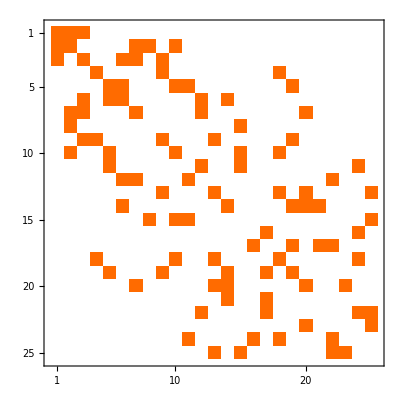
Adjacency matrix of orbit is: -Graphics-

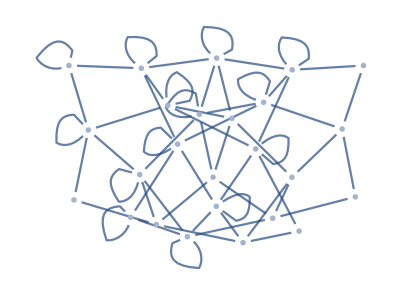

```mathematica
noqub=6;
myclass=6;

Print["First graph in orbit is: ",orbitsCigraphlist[[noqub]][[myclass]][[1]]]
Print["Number of graphs in Orbit is: ",Length@orbitsCigraphlist[[noqub]][[myclass]]]
Print["Adjacency matrix of orbit is: ",MatrixPlot@AdjacencyMatrix@orbitsCi[[noqub]][[myclass]]]

plotOrbitCi[noqub,myclass,"SpringElectricalEmbedding"]
```

## Print unlabelled graph state orbit adjacency matrices, ordered and grouped by edgecount

#### Plot Settings

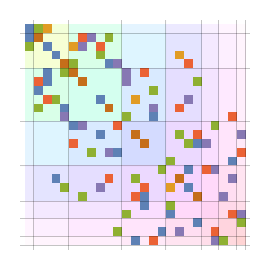
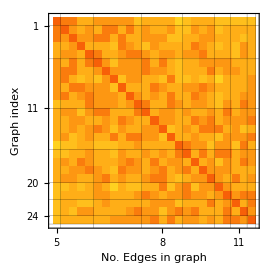
{-Graphics-,1 | RGBColor[0.368417, 0.506779, 0.709798]
2 | RGBColor[0.880722, 0.611041, 0.142051]
3 | RGBColor[0.560181, 0.691569, 0.194885]
4 | RGBColor[0.922526, 0.385626, 0.209179]
5 | RGBColor[0.528488, 0.470624, 0.701351]
6 | RGBColor[0.772079, 0.431554, 0.102387],-Graphics-,}

```mathematica
(*Adjust plot cosmetics*)
myframethickness=0.5;
myfontsize=10;
graphsize=270;

(*Adjust colour space for plots*)
satmod=0.17;
brightmod=1;

(*Difference in edge number required to be displayed on the plot*)
tickthresno=1;          (*in graph index*)
tickthresedge=1;     (*in edge number*)

plotOrbitMatrixCi[noqub,myclass]
```